# Allan Vriance-like Plot for DNA Seqence

理化学研究所・農業生物資源研究所　天野晃

## 目的

本研究の目的は、Allan分散分析のDNA塩基配列データへの応用可能性を探ることである。

時系列シークエンス解析の技術は、DNA塩基配列データによく用いられるが、Allan分散分析を用いたという報告はない。

## 方法論

### Allan分散分析

#### 概要

Allan分散分析の対象は発振器やセンサーからの時系列データである。

時間領域において評価対象となるモデルもしくはセンサーのノイズ成分の定量評価ができる。

Allan分散の値を時間領域ごとにプロットしたものがAllan分散プロットである。

周波数領域におけるフーリエ解析とは、相補的役割をなす。

#### 手順

ベクトルa = {a1, a2, a3, ...}とする。

時間幅wを設定する。

ベクトルaより幅wからなるすべてのサブリストを生成する。

すべての隣接するサブリスト間の平均差をとる(m番目とm+w番目のサブリストのそれぞれの平均値を求め、その差をとる)。

すべての平均差を2乗し、その平均に1/2を掛けた値を求める。これがAllan分散である。

上記1-4のステップをすべての可能なwにつき行う。

wを横軸座標として、対応するAllan分散の値を縦軸座標として両対数プロットを行ったものがAllan分散プロットである。

#### 例

```mathematica
allanVar[ylist_,w_]:=(1/2)Mean[(ListCorrelate[Append[PadRight[{-1},w],1],MovingAverage[ylist,w]])^2]
```

```mathematica
Manipulate[Module[{Ntot,opts,ylist,g1,g2,Npts,τdata,σdata,στdata},Ntot=5000;
opts=Sequence[Frame->True,Axes->False,Joined->True,GridLines->Automatic,BaseStyle->12,ImageSize->480];
ylist=RandomReal[NormalDistribution[0,a],Ntot]+b Cos[(2 π)/T Range[Ntot]]+d Range[Ntot];
g1=ListPlot[ylist,FrameLabel->{"t [s]","y(t)"},PlotRange->{All,{-0.4,0.4}},AspectRatio->0.17,opts];
Npts=30;
τdata=Union[Table[Round[10^((i-1) Log[10,1000]/Npts)],{i,1,Npts+1}]];
σdata=Sqrt[allanVar[ylist,#]]&/@τdata;
στdata=Transpose[{τdata,σdata}];
g2=Show[ListLogLogPlot[στdata,PlotMarkers->Automatic,FrameLabel->{"τ [s]","\!\(\*SubscriptBox[\(σ\), \(y\)]\)(τ)"},PlotRange->{All,{0.00009,0.2}},AspectRatio->0.48,opts,FrameTicks->{{1,10,100,1000},{{10^-4,"\!\(\*SuperscriptBox[\(10\), \(-4\)]\)"},{10^-3,"\!\(\*SuperscriptBox[\(10\), \(-3\)]\)"},{10^-2,"\!\(\*SuperscriptBox[\(10\), \(-2\)]\)"},{10^-1,"\!\(\*SuperscriptBox[\(10\), \(-1\)]\)"}},None,None}],LogLogPlot[b Sin[π τ/T]^2/(π τ/T),{τ,1,1000},PlotStyle->Directive[{Thick,Dashed,RGBColor[.49,0,0]}]],LogLogPlot[d τ/Sqrt[2],{τ,1,1000},PlotStyle->Directive[{Thick,Dashed,Darker@RGBColor[.6,.73,.36]}]]];
Column[{g1,g2}]],{{a,0.05,"white frequency noise amplitude"},0.01,0.1,Appearance->"Labeled"},{{b,0.012,"oscillation amplitude"},0,0.1,Appearance->"Labeled"},{{T,100,"oscillation period (s)"},10,1000,Appearance->"Labeled"},{{d,0.000005,"drift (1/s)"},0,0.0001,Appearance->"Labeled"},SaveDefinitions->True,TrackedSymbols:>{a,b,T,d}]
```

### Allan分散分析のDNA塩基配列への応用(オリゴヌクレオチド法)

なんらかの塩基配列間の”差”を定義することができれば、DNA塩基配列においてもAllan分散に相当する値が得られる。

塩基配列間の”差”は、”オリゴヌクレオチド頻度ベクトル間の距離”とすることができる。

#### 手順

塩基配列a = {a1, a2, a3, ...}とする(a1, a2, a3, ...は塩基)。

部分塩基配列幅wを設定する。

塩基配列aより幅wからなるすべての部分塩基配列を生成する。

すべての隣接する部分塩基配列間の距離をとる。

距離はオリゴヌクレオチド頻度ベクトルのユークリッド距離とする。

オリゴヌクレオチド頻度は部分配列においてとりうるすべてのオリゴヌクレオチド長nを考える。

その距離を2乗したものの平均に1/2を掛けた値を求める。これが”Allan分散様値”である。

上記1-4のステップをすべての可能なw、nにつき行う。

各nにつき、wを横軸座標として、対応するAllan分散様値を縦軸座標として(両対数)プロットを行ったものがAllan分散様プロットと定義できる。

### Allan分散分析のDNA塩基配列への応用(複素数法)

各塩基を、何らかの数値に置き換えることができるなら、直接、Allan分散分析が行える。

#### 手順

塩基配列a = {a1, a2, a3, ...}とする(a1, a2, a3, ...は塩基)。

各塩基を数値に置き換える。

A -> 1

C -> I

G -> -I

T -> -1

それ以外 -> 0

前述のAllan分散分析の手順を実行する。

## 検証: 提案方法の性質 - 完全な繰り返し配列

### 対象

Poly ACGT

500回繰り返し配列、2000塩基

### 方法

#### オリゴヌクレオチド法

幅w: 4 - 16

オリゴヌクレオチド長: 1 - 4

#### 複素数法

幅w: 1 - 40

通常プロット

### 結果

#### オリゴヌクレオチド法

```mathematica
{{, "n:1", "n:2", "n:3", "n:4"}, {4, 0., 0., 0., 0.}, {5, 1., 0., 1., 1.}, {6, 2., 1., 0., 1.}, {7, 1., 1., 1., 0.}, {8, 0., 0., 0., 0.}, {9, 1., 0., 1., 1.}, {10, 2., 1., 0., 1.}, {11, 1., 1., 1., 0.}, {12, 0., 0., 0., 0.}, {13, 1., 0., 1., 1.}, {14, 2., 1., 0., 1.}, {15, 1., 1., 1., 0.}, {16, 0., 0., 0., 0.}}
```

-Graphics3D-

#### 複素数法

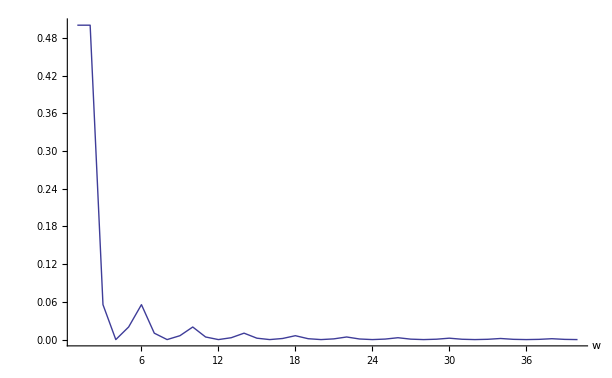

## 検証: 提案方法の性質 - ランダム配列

### 対象

2000塩基のランダム配列

メルセンヌ・ツイスタ: {1->A, 2->C, 3->G, 4->T}

### 方法

#### オリゴヌクレオチド法

幅w: 4 - 16

オリゴヌクレオチド長: 1 - 4

#### 複素数法

幅w: 1 - 40

通常プロット

### 結果

#### オリゴヌクレオチド法

-Graphics3D-

#### 複素数法

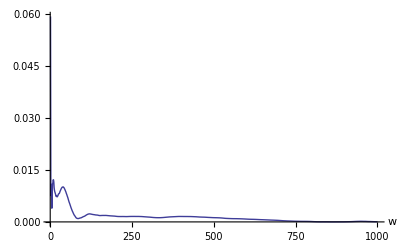

## 検証: 実データ - ファージX174

### 対象

PhiX174 DNA塩基配列: 5386塩基

### 方法

#### オリゴヌクレオチド法

幅w: 1 - 512

オリゴヌクレオチド長: 1 - 8

w < nの範囲 -> 0

#### 複素数法

幅w: 1 - 2000

通常プロット

### 結果

#### そのまえにフーリエ解析の結果

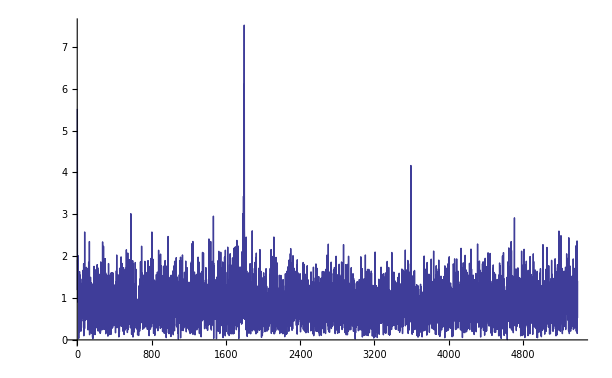

もっとも強度のある周波数は1798、これに対応するシグナルの長さ、つまり配列の長さは2.997。これは、コドンの長さ3と一致する。

#### オリゴヌクレオチド法

-Graphics3D-

#### 複素数法

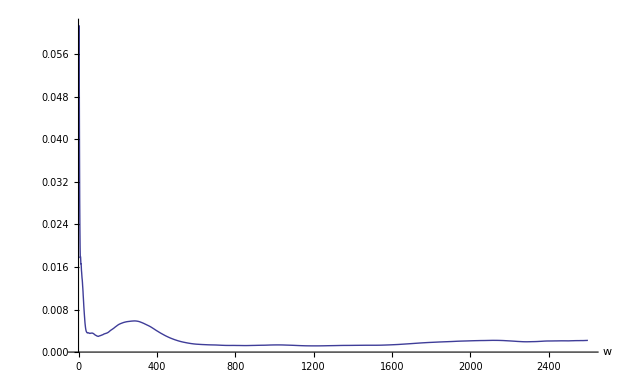

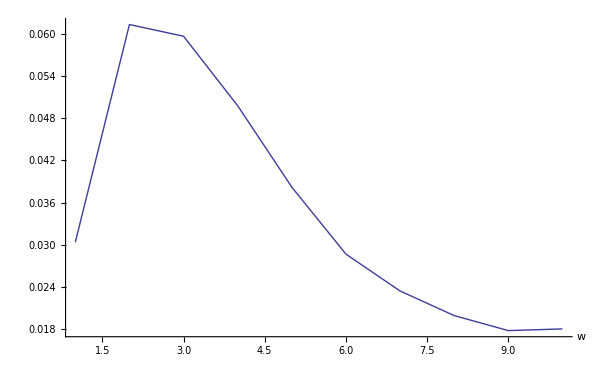

## まとめ

Allan分散は高い周波数領域、つまり短い時間領域に対して敏感であるため(ノイズ成分を過剰に評価するため)、短いパターンの繰り返しを検出するにはフーリエ解析が有利である。

逆に、複素数法では、低い周波数領域、つまり長い時間領域に対しては、フーリエ解析よりも適切な解析ができる可能性がある。

オリゴヌクレオチド法では、ランダム性が強調され、適切な解析を行えないと思われる。

用いたデータが少なかった。計算に時間が掛かったのが原因。今後は高速に計算するツールを開発する。

## 用語解説

フーリエ解析とは、相補的役割をなす -> 黒板で

隣接するサブリスト間の平均差 -> 黒板で

オリゴヌクレオチド頻度 -> 黒板で

コドン: アミノ酸を指定するDNA塩基の三つ組のパターン

## 謝辞

シュルンベルジェ株式会社　佐藤滋氏には、Allan分散の詳細を教授いただきました。感謝致します。

## 計算メモ

```mathematica
Get["/home/kamano/SCRIPT-MATHEMATICA/SCRIPTS/DNA_sequence_operations.txt"]
```

```mathematica
polyACGT=StringJoin[Table["ACGT",{500}]];
```

```mathematica
AbsoluteTiming[AllanDNA["ACGT",4,16,1,4]=Parallelize[Table[Mean[Map[Tr[(#[[1]]-#[[2]])^2]&,contactPair[Map[oligonucToVec[#,n]&,seqToSubseqs[polyACGT,w]],w]//N]]/2,{w,4,16,1},{n,1,4}]]]
```

LinkObject::linkd: Unable to communicate with closed link LinkObject["/usr/local/Wolfram/Mathematica/8.0/Executables/math -subkernel -noinit -mathlink", 18, 8].

LinkObject::linkd: Unable to communicate with closed link LinkObject["/usr/local/Wolfram/Mathematica/8.0/Executables/math -subkernel -noinit -mathlink", 19, 8].

LinkObject::linkd: Unable to communicate with closed link LinkObject["/usr/local/Wolfram/Mathematica/8.0/Executables/math -subkernel -noinit -mathlink", 20, 8].

General::stop: Further output of LinkObject :: linkd will be suppressed during this calculation.

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

{32.70263,{{0.,0.,0.,0.},{1.,0.,1.,1.},{2.,1.,0.,1.},{1.,1.,1.,0.},{0.,0.,0.,0.},{1.,0.,1.,1.},{2.,1.,0.,1.},{1.,1.,1.,0.},{0.,0.,0.,0.},{1.,0.,1.,1.},{2.,1.,0.,1.},{1.,1.,1.,0.},{0.,0.,0.,0.}}}

オリゴヌクレオチド法

```mathematica
TableForm[AllanDNA["ACGT",4,16,1,4],TableHeadings->{Table[n,{n,4,16}],{"n:1","n:2","n:3","n:4"}}]
```

| n:1 | n:2 | n:3 | n:4
4 | 0. | 0. | 0. | 0.
5 | 1. | 0. | 1. | 1.
6 | 2. | 1. | 0. | 1.
7 | 1. | 1. | 1. | 0.
8 | 0. | 0. | 0. | 0.
9 | 1. | 0. | 1. | 1.
10 | 2. | 1. | 0. | 1.
11 | 1. | 1. | 1. | 0.
12 | 0. | 0. | 0. | 0.
13 | 1. | 0. | 1. | 1.
14 | 2. | 1. | 0. | 1.
15 | 1. | 1. | 1. | 0.
16 | 0. | 0. | 0. | 0.

```mathematica
ListPlot3D[AllanDNA["ACGT",4,16,1,4],AxesLabel->{"n","w","σ"}]
```

-Graphics3D-

複素数法

```mathematica
allanVar[ylist_,w_]:=1/2 Mean[(ListCorrelate[Append[PadRight[{-1},w],1],MovingAverage[ylist,w]])^2]
```

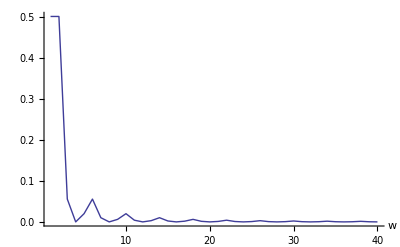

```mathematica
ListPlot[Table[allanVar[N[nucleotideToComplex[polyACGT]],n]//Abs,{n,1,40}],PlotRange->All,Joined->True,AxesLabel->{"w",None}]
```

ランダム塩基配列

```mathematica
SeedRandom[Method->"MersenneTwister"]
```

```mathematica
seqRand=StringJoin[Table[RandomInteger[{1,4}],{2000}]/.{1->"A",2->"C",3->"G",4->"T"}];
```

```mathematica
AbsoluteTiming[AllanDNA["seqRand",4,16,1,4]=Parallelize[Table[Mean[Map[Tr[(#[[1]]-#[[2]])^2]&,contactPair[Map[oligonucToVec[#,n]&,seqToSubseqs[seqRand,w]],w]//N]]/2,{w,4,16,1},{n,1,4}]]]
```

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

{34.76004,{{3.04064,2.87005,1.97341,0.992975},{3.86238,3.82772,2.96735,1.99749},{4.73303,4.81297,3.96933,3.01458},{5.57625,5.79618,4.97131,4.02567},{6.45592,6.77179,5.99496,5.04282},{7.36409,7.73777,7.00807,6.06051},{8.30288,8.71126,8.02675,7.08582},{9.238,9.70187,9.06215,8.11319},{10.1265,10.6859,10.0855,9.13961},{11.0116,11.6835,11.1205,10.1711},{11.8312,12.6711,12.148,11.2027},{12.6819,13.658,13.1689,12.2293},{13.5561,14.6435,14.1803,13.2529}}}

```mathematica
ListPlot3D[AllanDNA["seqRand",4,16,1,4],AxesLabel->{"n","w","σ"}]
```

-Graphics3D-

```mathematica
ListPlot[Table[allanVar[N[nucleotideToComplex[seqRand]],n]//Abs,{n,1,1000}],PlotRange->All,Joined->True,AxesLabel->{"w",None}]
```

-Graphics-

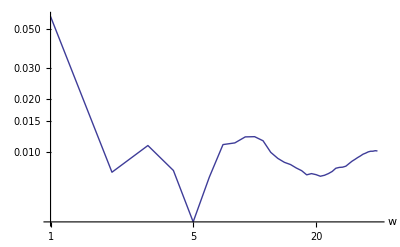

```mathematica
ListLogLogPlot[Table[allanVar[N[nucleotideToComplex[seqRand]],n]//Abs,{n,1,40}],PlotRange->All,Joined->True,AxesLabel->{"w",None}]
```

ファージシークエンス

```mathematica
quedir="/home/kamano/TEST_COLLECTION/AllanVarianceLike-Plot/bin/"
```

/home/kamano/TEST_COLLECTION/AllanVarianceLike-Plot/bin/

```mathematica
(que[1]=Get[quedir<>"allanDNA_x174.4.128.1.4.out.list"])//Dimensions
(que[1]=Join[{{0,0,0,0},{0,0,0,0},{0,0,0,0}},que[1]])//Dimensions
```

{125,4}

{128,4}

```mathematica
(que[2]=Get[quedir<>"allanDNA_x174.129.256.1.4.out.list"])//Dimensions
```

{128,4}

```mathematica
(que[3]=Get[quedir<>"allanDNA_x174.257.384.1.4.out.list"])//Dimensions
```

{128,4}

```mathematica
(que[4]=Get[quedir<>"allanDNA_x174.385.512.1.4.out.list"])//Dimensions
```

{128,4}

```mathematica
(que[8]=Get[quedir<>"allanDNA_x174.8.128.5.8.out.list"])//Dimensions
(que[8]=Join[Table[0,{7},{4}],que[8]])//Dimensions
```

{121,4}

{128,4}

```mathematica
(que[5]=Get[quedir<>"allanDNA_x174.129.256.5.8.out.list"])//Dimensions
```

{128,4}

```mathematica
(que[6]=Get[quedir<>"allanDNA_x174.257.384.5.8.out.list"])//Dimensions
```

{128,4}

```mathematica
(que[7]=Get[quedir<>"allanDNA_x174.385.512.5.8.out.list"])//Dimensions
```

{128,4}

```mathematica
(que["1-4"]=Join[que[1],que[2],que[3],que[4]])//Dimensions
```

{512,4}

```mathematica
(que["5-8"]=Join[que[8],que[5],que[6],que[7]])//Dimensions
```

{512,4}

```mathematica
(que["All"]=Transpose[Join[Transpose[que["1-4"]],Transpose[que["5-8"]]]])//Dimensions
```

{512,8}

```mathematica
ListPlot3D[que["All"],AxesLabel->{"n","w","σ"}]
```

-Graphics3D-

```mathematica
seqX174=Import["/BANK/SEQUENCE/genome/ncbi/genomes/_Phage/phiX174.fasta"][[1]];
```

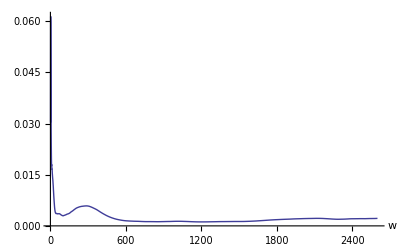

```mathematica
ListPlot[Table[allanVar[N[nucleotideToComplex[seqX174]],n]//Abs,{n,1,2600}],PlotRange->All,Joined->True,AxesLabel->{"w",None}]
```

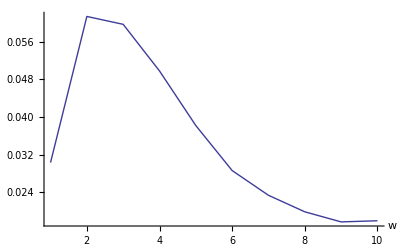

```mathematica
ListPlot[Table[allanVar[N[nucleotideToComplex[seqX174]],n]//Abs,{n,1,10}],PlotRange->All,Joined->True,AxesLabel->{"w",None}]
```

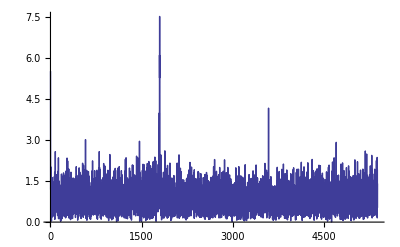

```mathematica
ListPlot[Fourier[N[nucleotideToComplex[seqX174]]]//Abs,Joined->True,PlotRange->All]
```